```mathematica
<<QINisq`
HSD[ρ_,σ_]:=Tr[MatrixPower[ρ-σ,2]];
```

Package QI version 0.4.39 (last modification: 13/02/2017).

Package QIExtras 0.0.12 (last modification: 12/04/2021).

Package QINisq 0.0.7 (last modification: 28/05/2021).

## Two-qubit X-MEMS

```mathematica
f[γ_]:=If[γ<=1/3,1/3,γ];
g[γ_]:=If[γ<=1/3,1/3,1-2γ];
```

```mathematica
ρ=({{f, 0, 0, α+ⅈ β}, {0, g, 0, 0}, {0, 0, 0, 0}, {α-ⅈ β, 0, 0, f}});
σ=({{a/2, 0, 0, c+ⅈ d}, {0, b, 0, 0}, {0, 0, 1-a-b, 0}, {c-ⅈ d, 0, 0, a/2}});
HSD[ρ_,σ_]:=Tr[MatrixPower[ρ-σ,2]];
```

```mathematica
dd=HSD[ρ,σ]//Simplify
```

(-1+a+b)^2+1/2 (a-2 f)^2+(b-g)^2+2 (c^2+d^2-2 c α+α^2-2 d β+β^2)

### Separability condition

```mathematica
E1=c^2+d^2-b(1-a-b)
```

-((1-a-b) b)+c^2+d^2

### Segment 1

```mathematica
L=dd+λ E1/.{f->1/3,g->1/3}//FullSimplify
L1=D[L,a]//FullSimplify
L2=D[L,b]//FullSimplify
L3=D[L,c]//FullSimplify
L4=D[L,d]//FullSimplify
```

1/2 (-2/3+a)^2+(-1/3+b)^2+(-1+a+b)^2+2 ((c-α)^2+(d-β)^2)+(b (-1+a+b)+c^2+d^2) λ

-8/3+3 a+b (2+λ)

-8/3-λ+a (2+λ)+2 b (2+λ)

-4 α+2 c (2+λ)

-4 β+2 d (2+λ)

```mathematica
sol=Solve[{L1==0,L2==0,L3==0,L4==0,E1==0},{a,b,c,d,λ}]//FullSimplify
Simplify[Reduce[{L1==0,L2==0,L3==0,E1==0},{a,b,c,d,λ}],{0<=a<=1,0<=b<=1,0<=a+b<=1,0<=√(c^2+d^2)<=a/2,0<=√(α^2+β^2)<=1/3}]
```

{{a→1/9 (7-√(1+36 α^2+36 β^2)),b→1/18 (3+2/(√(1+36 α^2+36 β^2))+√(1+36 α^2+36 β^2)),c→1/3 α (1+2/(√(1+36 α^2+36 β^2))),d→1/3 β (1+2/(√(1+36 α^2+36 β^2))),λ→(4+48 α^2+48 β^2-4 √(1+36 α^2+36 β^2))/(-1+12 α^2+12 β^2)},{a→1/9 (7+√(1+36 α^2+36 β^2)),b→1/18 (3-2/(√(1+36 α^2+36 β^2))-√(1+36 α^2+36 β^2)),c→1/3 α (1-2/(√(1+36 α^2+36 β^2))),d→1/3 β (1-2/(√(1+36 α^2+36 β^2))),λ→(4 (1+12 α^2+12 β^2+√(1+36 α^2+36 β^2)))/(-1+12 α^2+12 β^2)}}

9 a≠7&&b==(8-17 a+9 a^2)/(14-18 a)&&c==3 (-1+a+2 b) α&&(6 d+√(18 a^2 (1+18 α^2)-2 a (17+288 α^2)+4 (4+63 α^2-9 b^2 (1+36 α^2)+b (2+72 α^2)))==0||√(18 a^2 (1+18 α^2)-2 a (17+288 α^2)+4 (4+63 α^2-9 b^2 (1+36 α^2)+b (2+72 α^2)))==6 d)&&a≠1&&λ==(8-12 a)/(3-3 a)

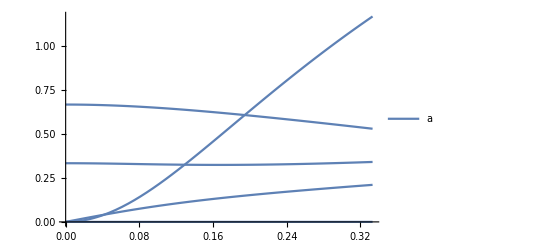

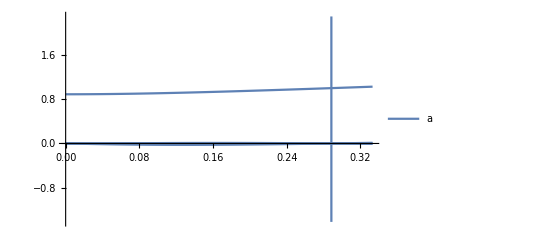

```mathematica
Plot[Evaluate@sol[[1,All,2]]/.β->0,{α,0,1/3},PlotLegends->{a,b,c,d,λ}]
Plot[Evaluate@sol[[2,All,2]]/.β->0,{α,0,1/3},PlotLegends->{a,b,c,d,λ}]
```

```mathematica
final=dd/.sol[[1]]/.{f->1/3,g->1/3}//PowerExpand//FullSimplify
```

-2/27 (-1-18 α^2-18 β^2+√(1+36 α^2+36 β^2))

### Segment 2

```mathematica
M=dd+λ E1/.{f->e,g->1-2e}//FullSimplify
M1=D[M,a]//FullSimplify
M2=D[M,b]//FullSimplify
M3=D[M,c]//FullSimplify
M4=D[M,d]//FullSimplify
```

(-1+a+b)^2+1/2 (a-2 e)^2+(-1+b+2 e)^2+2 ((c-α)^2+(d-β)^2)+(b (-1+a+b)+c^2+d^2) λ

3 a-2 (1+e)+b (2+λ)

-4+4 e-λ+a (2+λ)+2 b (2+λ)

-4 α+2 c (2+λ)

-4 β+2 d (2+λ)

```mathematica
sol2=Solve[{M1==0,M2==0,M3==0,M4==0,E1==0},{a,b,c,d,λ}]//FullSimplify
Simplify[Reduce[{M1==0,M2==0,M3==0,M4==0,E1==0},{a,b,c,d,λ}],{0<=a<=1,0<=b<=1,0<=a+b<=1,0<=√(c^2+d^2)<=a/2,1/3<=√(α^2+β^2)<=1/2}]//FullSimplify
```

{{a→1/3 (1+4 e-(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/(3+12 (-1+e) e+4 α^2+4 β^2)),b→1/6 (3-6 e+(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/(1+4 (-1+e) e+4 α^2+4 β^2)),c→1/3 α (1-(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (1+4 (-1+e) e+4 α^2+4 β^2))+(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (3+12 (-1+e) e+4 α^2+4 β^2))),d→1/3 β (1-(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (1+4 (-1+e) e+4 α^2+4 β^2))+(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (3+12 (-1+e) e+4 α^2+4 β^2))),λ→(4 (288 e^3-144 e^4+24 e (3+4 α^2+4 β^2)-(3+4 α^2+4 β^2)^2-24 e^2 (9+4 α^2+4 β^2)+3 √((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2)-6 e √((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2)))/((3+12 (-1+e) e-4 α^2-4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2))},{a→1/3 (1+4 e+(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/(3+12 (-1+e) e+4 α^2+4 β^2)),b→1/2-e-(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/(6 (1+4 (-1+e) e+4 α^2+4 β^2)),c→1/3 α (1+(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (1+4 (-1+e) e+4 α^2+4 β^2))-(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (3+12 (-1+e) e+4 α^2+4 β^2))),d→1/3 β (1+(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (1+4 (-1+e) e+4 α^2+4 β^2))-(√((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2))/((-1+2 e) (3+12 (-1+e) e+4 α^2+4 β^2))),λ→(4 (288 e^3-144 e^4+24 e (3+4 α^2+4 β^2)-(3+4 α^2+4 β^2)^2-24 e^2 (9+4 α^2+4 β^2)-3 √((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2)+6 e √((1+4 (-1+e) e+4 α^2+4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2)^2)))/((3+12 (-1+e) e-4 α^2-4 β^2) (3+12 (-1+e) e+4 α^2+4 β^2))}}

(2 e==1&&((a==1&&b==0&&(c≠0||d==0)&&(c==0||d==-ⅈ c||d==ⅈ c)&&(c==0||2+λ==0)&&α==0&&β==0)||(a+2 b==1&&3 c==α&&3 d==β&&3 a+2 √(α^2+β^2)==3&&λ==4&&a≠1)))||(b==(6+9 a (-1+2 e)-6 e (1+2 e)+4 α^2+4 β^2)/(6-18 a+24 e)&&c+((-1+a+2 b) α)/(-1+2 e)==0&&d+((-1+a+2 b) β)/(-1+2 e)==0&&λ==(4 (a-2 e))/(-1+a)&&3 a≠1+4 e&&(3 a+√(1+4 (-1+e) e+4 α^2+4 β^2)==1+4 e||1+4 e+√(1+4 (-1+e) e+4 α^2+4 β^2)==3 a))

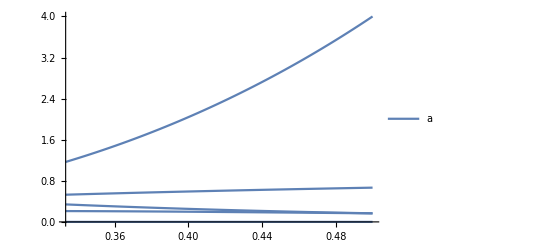

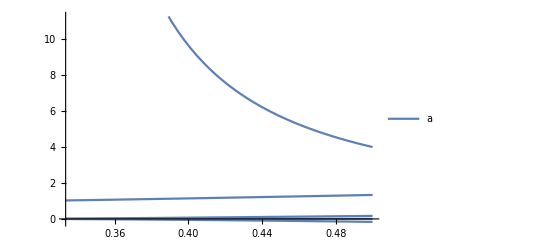

```mathematica
Plot[Evaluate@sol2[[1,All,2]]/.{β->0,e->α},{α,1/3,1/2},PlotLegends->{a,b,d,λ}]
Plot[Evaluate@sol2[[2,All,2]]/.{β->0,e->α},{α,1/3,1/2},PlotLegends->{a,b,d,λ}]
```

```mathematica
final2=dd/.sol2[[2]]/.{f->e,g->1-2e}//PowerExpand//FullSimplify
```

1/3 (8 e^2-4 e (2+√(1+4 (-1+e) e+4 α^2+4 β^2))+2 (1+2 α^2+2 β^2+√(1+4 (-1+e) e+4 α^2+4 β^2)))

```mathematica
-4 e (2+√(1+4 (-1+e) e+4 α^2+4 β^2))/.{e->√(α^2+β^2)}//FullSimplify
```

-4 √(α^2+β^2) (2+√(1+8 α^2+8 β^2-4 √(α^2+β^2)))

```mathematica
1/3(8 γ^2-4γ(2+√(1-4γ+8 γ^2))+2(1+2 γ^2+√(1-4γ+8 γ^2)))//PowerExpand//FullSimplify
```

2/3 (1+6 γ^2+√(1-4 γ+8 γ^2)-2 γ (2+√(1-4 γ+8 γ^2)))

### Minimisation

```mathematica
tab=Table[{x,NMinimize[{dd/.{f->f[x],g->g[x],γ->x},E1<=0,0<=a<=1,0<=b<=1,0<=a+b<=1,0<=d<=a/2},{a,b,d}][[1]]},{x,0,1/2,0.01}]
```

{{0.,2.72881×10^-16},{0.01,1.15991×10^-7},{0.02,1.82598×10^-6},{0.03,9.56568×10^-6},{0.04,0.0000298659},{0.05,0.0000718038},{0.06,0.000146191},{0.07,0.000265204},{0.08,0.000441928},{0.09,0.00068994},{0.1,0.00102293},{0.11,0.00145443},{0.12,0.0019975},{0.13,0.00266466},{0.14,0.00346769},{0.15,0.0044176},{0.16,0.0055246},{0.17,0.0067981},{0.18,0.0082467},{0.19,0.00987828},{0.2,0.0117},{0.21,0.0137184},{0.22,0.0159393},{0.23,0.0183681},{0.24,0.0210097},{0.25,0.0238685},{0.26,0.0269483},{0.27,0.0302529},{0.28,0.0337855},{0.29,0.037549},{0.3,0.0415462},{0.31,0.0457795},{0.32,0.0502512},{0.33,0.0549632},{0.34,0.0620732},{0.35,0.0710179},{0.36,0.0808614},{0.37,0.0916465},{0.38,0.103414},{0.39,0.116203},{0.4,0.130051},{0.41,0.14499},{0.42,0.161056},{0.43,0.178277},{0.44,0.196682},{0.45,0.216297},{0.46,0.237148},{0.47,0.259257},{0.48,0.282644},{0.49,0.307331},{0.5,0.333333}}

```mathematica
γlist=Table[i,{i,0,0.5,0.01}];
python={0.0007775515283585666,0.00011786038795402742,0.00017971056577525957,2.5536857252150824*10^-5,3.76698840922618*10^-5,7.561616823592576*10^-5,0.00014636609997809025,0.00026538596763869826,0.0004419345915541717,0.0006899592013235312,0.0010229373863683833,0.0014544383124890368,0.001997502425982512,0.0026646659586619936,0.0034676899866099564,0.004417605954380788,0.005524607917074875,0.006798100338125668,0.008246701393451628,0.00987828385071232,0.011700011934779875,0.01371838287353566,0.015939311694915137,0.018368149810603973,0.021009742759846017,0.02386847414117088,0.02694833194402424,0.030252916247217376,0.03378549227849469,0.03754903574615586,0.04154622649935902,0.045779526597486735,0.050251159881222314,0.05496315350178349,0.06207322916094882,0.0710178765552052,0.0808613877506349,0.0916465479736208,0.10341423891780388,0.1162033143236152,0.1300505194268743,0.14499049763570823,0.161055756364064,0.17827672406439907,0.19668180466439897,0.21629743549446512,0.23714817823131448,0.25925681920166727,0.2826444555423597,0.3073306176948828,0.333333335315828};
data=Table[{γlist[[i]],python[[i]]},{i,1,51}]
```

{{0.,0.000777552},{0.01,0.00011786},{0.02,0.000179711},{0.03,0.0000255369},{0.04,0.0000376699},{0.05,0.0000756162},{0.06,0.000146366},{0.07,0.000265386},{0.08,0.000441935},{0.09,0.000689959},{0.1,0.00102294},{0.11,0.00145444},{0.12,0.0019975},{0.13,0.00266467},{0.14,0.00346769},{0.15,0.00441761},{0.16,0.00552461},{0.17,0.0067981},{0.18,0.0082467},{0.19,0.00987828},{0.2,0.0117},{0.21,0.0137184},{0.22,0.0159393},{0.23,0.0183681},{0.24,0.0210097},{0.25,0.0238685},{0.26,0.0269483},{0.27,0.0302529},{0.28,0.0337855},{0.29,0.037549},{0.3,0.0415462},{0.31,0.0457795},{0.32,0.0502512},{0.33,0.0549632},{0.34,0.0620732},{0.35,0.0710179},{0.36,0.0808614},{0.37,0.0916465},{0.38,0.103414},{0.39,0.116203},{0.4,0.130051},{0.41,0.14499},{0.42,0.161056},{0.43,0.178277},{0.44,0.196682},{0.45,0.216297},{0.46,0.237148},{0.47,0.259257},{0.48,0.282644},{0.49,0.307331},{0.5,0.333333}}

```mathematica
(data-tab)[[All,2]]
```

{0.000777552,0.000117744,0.000177885,0.0000159712,7.80401×10^-6,3.81242×10^-6,1.75003×10^-7,1.82101×10^-7,6.14233×10^-9,1.91317×10^-8,7.4726×10^-9,1.31527×10^-8,1.72241×10^-9,7.60761×10^-9,2.11346×10^-9,6.41287×10^-9,5.27895×10^-9,4.49195×10^-9,1.4347×10^-9,2.48636×10^-9,6.99116×10^-9,3.49635×10^-9,2.5506×10^-9,4.33894×10^-9,6.93732×10^-9,3.36268×10^-9,4.55466×10^-9,3.70887×10^-9,4.1731×10^-9,8.81586×10^-9,6.03817×10^-9,6.5607×10^-9,8.4664×10^-9,8.26049×10^-10,6.77028×10^-9,4.89223×10^-9,1.2137×10^-8,6.5953×10^-9,-1.68572×10^-9,2.2041×10^-8,1.42035×10^-8,4.72192×10^-8,9.05331×10^-9,6.65475×10^-10,-6.48825×10^-9,-1.48687×10^-8,8.67733×10^-8,2.51843×10^-10,-1.94442×10^-8,-1.58615×10^-8,-1.0049×10^-7}

### Plot

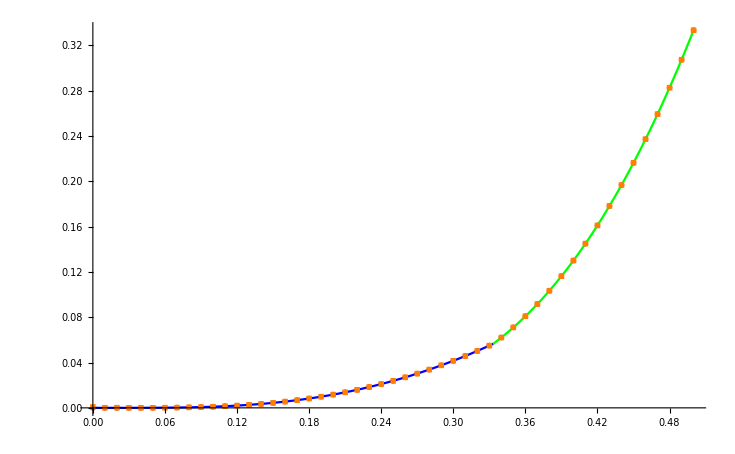

```mathematica
Show[ListPlot[tab, PlotStyle->Red,PlotMarkers->●], Plot[final,{γ,0,1/3},PlotStyle->Blue], Plot[final2,{γ,1/3,1/2},PlotStyle->Green],ListPlot[data, PlotStyle->Orange,PlotMarkers->■]]
```

## Three-qubit X-MEMS

```mathematica
f[γ_]:=If[γ<=1/5,1/5,γ];
g[γ_]:=If[γ<=1/5,1/5,(1-2γ)/3];
```

```mathematica
ρ=({{f, 0, 0, 0, 0, 0, 0, γ}, {0, g, 0, 0, 0, 0, 0, 0}, {0, 0, g, 0, 0, 0, 0, 0}, {0, 0, 0, g, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {γ, 0, 0, 0, 0, 0, 0, f}});
σ=({{a/2, 0, 0, 0, 0, 0, 0, d}, {0, b/3, 0, 0, 0, 0, 0, 0}, {0, 0, b/3, 0, 0, 0, 0, 0}, {0, 0, 0, b/3, 0, 0, 0, 0}, {0, 0, 0, 0, (1-a-b)/3, 0, 0, 0}, {0, 0, 0, 0, 0, (1-a-b)/3, 0, 0}, {0, 0, 0, 0, 0, 0, (1-a-b)/3, 0}, {d, 0, 0, 0, 0, 0, 0, a/2}});
HSD[ρ_,σ_]:=Tr[MatrixPower[ρ-σ,2]];
```

```mathematica
dd=HSD[ρ,σ]
```

1/3 (-1+a+b)^2+2 (-a/2+f)^2+3 (-b/3+g)^2+2 (-d+γ)^2

### Separability condition

```mathematica
Eigenvalues[PartialTranspose[σ,{2,2,2},{1}]]//PowerExpand//FullSimplify
```

{a/2,a/2,b/3,b/3,1/3 (1-a-b),1/3 (1-a-b),1/6 (1-a-√((-1+a+2 b)^2+36 d^2)),1/6 (1-a+√((-1+a+2 b)^2+36 d^2))}

```mathematica
E1=9 d^2-b(1-a-b)
```

-((1-a-b) b)+9 d^2

### Segment 1

```mathematica
L=dd+λ E1/.{f->1/5,g->1/5}//FullSimplify
L1=D[L,a]//FullSimplify
L2=D[L,b]//FullSimplify
L3=D[L,d]//FullSimplify
```

1/50 (2-5 a)^2+1/75 (3-5 b)^2+1/3 (-1+a+b)^2+2 (d-γ)^2+b (-1+a+b) λ+9 d^2 λ

-16/15+(5 a)/3+b (2/3+λ)

2/15 (-8+5 a+10 b)+(-1+a+2 b) λ

-4 γ+2 d (2+9 λ)

```mathematica
sol=Solve[{L1==0,L2==0,L3==0,E1==0},{a,b,d,λ}]
Simplify[Reduce[{L1==0,L2==0,L3==0,E1==0},{a,b,d,λ}],{0<=a<=1,0<=b<=1,0<=a+b<=1,0<=d<=a/2,0<=γ<=1/5}]
```

(1)
 |  |  |  |

(a==Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,1]||a==Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,2]||a==Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,3]||a==Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,4])&&68658 a+105625 a^3+36 (8 b+325 γ^2)==10528+149175 a^2+22500 a γ^2&&65 a≠29&&d==(5 (-1+a) γ)/(-29+65 a)&&a≠1&&λ==(8 (-2+5 a))/(15 (-1+a))

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

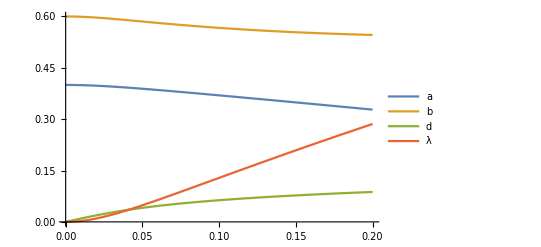

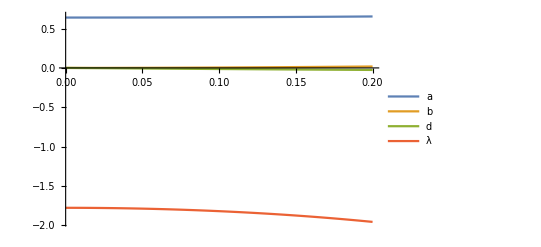

-Graphics-

-Graphics-

```mathematica
aa=Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,1];
Plot[{aa,1/288 (10528-68658 a+149175 a^2-105625 a^3-11700 γ^2+22500 a γ^2)/.a->aa,(5 (-1+a) γ)/(-29+65 a)/.a->aa,(8 (-2+5 a))/(15 (-1+a))/.a->aa},{γ,0,1/5},PlotLegends->{a,b,d,λ}]
aa=Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,2];
Plot[{aa,1/288 (10528-68658 a+149175 a^2-105625 a^3-11700 γ^2+22500 a γ^2)/.a->aa,(5 (-1+a) γ)/(-29+65 a)/.a->aa,(8 (-2+5 a))/(15 (-1+a))/.a->aa},{γ,0,1/5},PlotLegends->{a,b,d,λ}]
aa=Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,3];
Plot[{aa,1/288 (10528-68658 a+149175 a^2-105625 a^3-11700 γ^2+22500 a γ^2)/.a->aa,(5 (-1+a) γ)/(-29+65 a)/.a->aa,(8 (-2+5 a))/(15 (-1+a))/.a->aa},{γ,0,1/5},PlotLegends->{a,b,d,λ}]
aa=Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,4];
Plot[{aa,1/288 (10528-68658 a+149175 a^2-105625 a^3-11700 γ^2+22500 a γ^2)/.a->aa,(5 (-1+a) γ)/(-29+65 a)/.a->aa,(8 (-2+5 a))/(15 (-1+a))/.a->aa},{γ,0,1/5},PlotLegends->{a,b,d,λ}]
```

```mathematica
aa=Root[26912-30420 γ^2+(-229970+117000 γ^2) #1+(730425-112500 γ^2) #1^2-1020500 #1^3+528125 #1^4&,1];
dd/.{f->1/5,g->1/5,b->1/288 (10528-68658 a+149175 a^2-105625 a^3-11700 γ^2+22500 a γ^2),d->(5 (-1+a) γ)/(-29+65 a),λ->(8 (-2+5 a))/(15 (-1+a))}//FullSimplify
```

1/50 (2-5 a)^2+2 (γ-(5 (-1+a) γ)/(-29+65 a))^2+1/6220800(-51776+58500 γ^2+5 a (68658+325 a (-459+325 a)-22500 γ^2))^2+1/248832 25 (a (13674+65 a (-459+325 a)-4500 γ^2)+4 (-512+585 γ^2))^2

```mathematica
final=dd/.sol[[2]]/.{f->1/5,g->1/5}
```

3 (1/5+1/3 (-267/520+1/2 √1-1/2 √1))^2+2 (1/5-1/1)^2+1/3 (1)^2+2 (γ-1/1)^2
 |  |  |  |

### Segment 2

```mathematica
M=dd+λ E1/.{f->γ,g->(1-2γ)/3}//FullSimplify
M1=D[M,a]//FullSimplify
M2=D[M,b]//FullSimplify
M3=D[M,d]//FullSimplify
```

1/3 (-1+a+b)^2+1/2 (a-2 γ)^2+2 (d-γ)^2+1/3 (-1+b+2 γ)^2+b (-1+a+b) λ+9 d^2 λ

a+2/3 (-1+a+b)-2 γ+b λ

2/3 (a+2 (-1+b+γ))+(-1+a+2 b) λ

-4 γ+2 d (2+9 λ)

```mathematica
sol2=Solve[{M1==0,M2==0,M3==0,E1==0},{a,b,d,λ}]
Simplify[Reduce[{M1==0,M2==0,M3==0,E1==0},{a,b,d,λ}],{0<=a<=1,0<=b<=1,0<=a+b<=1,0<=d<=a/2,1/5<=γ<=1/2}]
```

(1)
 |  |  |  |

(a==Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,1]||a==Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,2]||a==Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,3]||a==Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,4])&&5 a≠1+8 γ&&b==-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))&&13 a≠1&&d==(4+16 a-65 a^2-4 b-47 γ+227 a γ+8 b γ-168 γ^2)/(1-13 a)&&a≠1&&λ==(8 (a-2 γ))/(3 (-1+a))

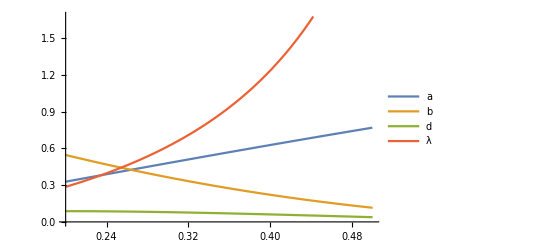

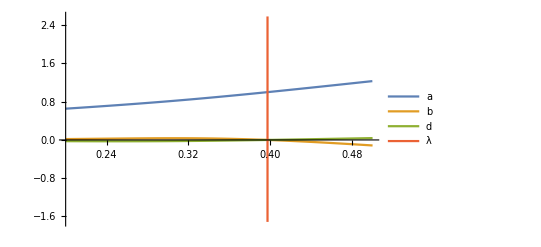

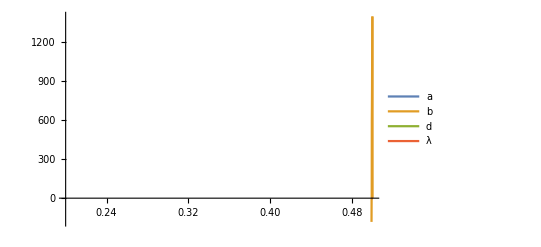

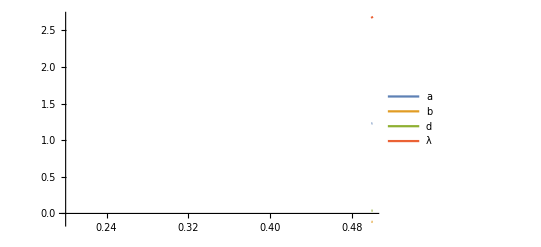

```mathematica
aa=Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,1];
Plot[{aa,-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(4+16 a-65 a^2-4 b-47 γ+227 a γ+8 b γ-168 γ^2)/(1-13 a)/.b->-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(8 (a-2 γ))/(3 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
aa=Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,2];
Plot[{aa,-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(4+16 a-65 a^2-4 b-47 γ+227 a γ+8 b γ-168 γ^2)/(1-13 a)/.b->-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(8 (a-2 γ))/(3 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
aa=Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,3];
Plot[{aa,-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(4+16 a-65 a^2-4 b-47 γ+227 a γ+8 b γ-168 γ^2)/(1-13 a)/.b->-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(8 (a-2 γ))/(3 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
aa=Root[20 γ+984 γ^2+13824 γ^3+32256 γ^4+(-10-1080 γ-23280 γ^2-80640 γ^3) #1+(285+12900 γ+73560 γ^2) #1^2+(-2340-29120 γ) #1^3+4225 #1^4&,4];
Plot[{aa,-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(4+16 a-65 a^2-4 b-47 γ+227 a γ+8 b γ-168 γ^2)/(1-13 a)/.b->-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ))/.a->aa,(8 (a-2 γ))/(3 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
```

```mathematica
dd/.{f->γ,g->(1-2γ)/3,b->-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ)),d->1/(1-13 a)(4+16 a-65 a^2-4 b-47 γ+227 a γ+8 b γ-168 γ^2)/.b->-((-1+a) (-2+5 a-6 γ))/(2 (-1+5 a-8 γ)),λ->(8 (a-2 γ))/(3 (-1+a))}//Expand//FullSimplify
```

1/(3 (1-13 a)^2 (1-5 a+8 γ)^2)2 (5 (1-13 a)^2 a^2 (61-302 a+380 a^2)-20 a (-1+13 a) (-61+a (1941+a (-9575+12867 a))) γ+4 (305+a (-25820+a (478878+5 a (-481612+704485 a)))) γ^2-128 (-495+a (17852+a (-127894+239345 a))) γ^3+64 (15593+a (-210154+565937 a)) γ^4-387072 (-11+57 a) γ^5+5419008 γ^6)

```mathematica
final2=dd/.sol2[[2]]/.{f->γ,g->(1-2γ)/3}
```

3 (1/3 (1-2 γ)+1/3 (1))^2+2 (γ-1/(2 1))^2+1/3 (6+1)^2+2 (γ-1/1)^2
 |  |  |  |

### Minimisation

```mathematica
tab=Table[{x,Minimize[{dd/.{f->f[x],g->g[x],γ->x},E1<=0,0<=a+b<=1,0<=a<=1,0<=b<=1,0<=d<=a/2},{a,b,d}][[1]]},{x,0,1/2,0.01}]
```

{{0.,3.91261×10^-18},{0.01,1.17556×10^-6},{0.02,0.0000176686},{0.03,0.0000827045},{0.04,0.000236618},{0.05,0.000518874},{0.06,0.000963761},{0.07,0.00160001},{0.08,0.00245124},{0.09,0.00353696},{0.1,0.00487332},{0.11,0.00647381},{0.12,0.00834983},{0.13,0.010511},{0.14,0.0129657},{0.15,0.015721},{0.16,0.0187832},{0.17,0.0221576},{0.18,0.0258492},{0.19,0.0298621},{0.2,0.0342},{0.21,0.0396693},{0.22,0.0456412},{0.23,0.0521294},{0.24,0.0591469},{0.25,0.0667065},{0.26,0.0748202},{0.27,0.0834999},{0.28,0.0927566},{0.29,0.102601},{0.3,0.113045},{0.31,0.124097},{0.32,0.135769},{0.33,0.148069},{0.34,0.161007},{0.35,0.174592},{0.36,0.188833},{0.37,0.203738},{0.38,0.219317},{0.39,0.235577},{0.4,0.252527},{0.41,0.270174},{0.42,0.288525},{0.43,0.307588},{0.44,0.327371},{0.45,0.347879},{0.46,0.36912},{0.47,0.3911},{0.48,0.413826},{0.49,0.437304},{0.5,0.461538}}

```mathematica
γlist=Table[i,{i,0,0.5,0.01}];
python={8.673557139182718*10^-8,0.0001756036398373184,0.0006547606116350524,0.001113441825562611,0.001809140403077336,0.0022230968883197866,0.002802425353232607,0.0039843944461276926,0.004302254694467211,0.00353994741203123,0.004878034788128538,0.006481063458371017,0.008360578892572912,0.010526502671766245,0.012987174074830963,0.015750111518035792,0.018821781483947086,0.02220764000590925,0.025912851892011257,0.02994192673683732,0.0342988448466538,0.0396736503584903,0.04567398971774678,0.05230558210676189,0.05957457815881045,0.06748689599786162,0.07604862268897926,0.08526584021188045,0.09514503998854462,0.1056923787685115,0.11691428741927812,0.12881693484306955,0.14140595444781115,0.15468669190851247,0.16866408824893675,0.183342084310972,0.19872700197453527,0.21481194099401923,0.2316066565145549,0.24907851634476097,0.257148664427986,0.27426964966790635,0.2923103189231486,0.31108243040855266,0.330582399071391,0.3508183287057656,0.3717990418295776,0.39352883462716126,0.4160167284327532,0.43926931586625617,0.46328982187231366};
data=Table[{γlist[[i]],python[[i]]},{i,1,51}]
```

{{0.,8.67356×10^-8},{0.01,0.000175604},{0.02,0.000654761},{0.03,0.00111344},{0.04,0.00180914},{0.05,0.0022231},{0.06,0.00280243},{0.07,0.00398439},{0.08,0.00430225},{0.09,0.00353995},{0.1,0.00487803},{0.11,0.00648106},{0.12,0.00836058},{0.13,0.0105265},{0.14,0.0129872},{0.15,0.0157501},{0.16,0.0188218},{0.17,0.0222076},{0.18,0.0259129},{0.19,0.0299419},{0.2,0.0342988},{0.21,0.0396737},{0.22,0.045674},{0.23,0.0523056},{0.24,0.0595746},{0.25,0.0674869},{0.26,0.0760486},{0.27,0.0852658},{0.28,0.095145},{0.29,0.105692},{0.3,0.116914},{0.31,0.128817},{0.32,0.141406},{0.33,0.154687},{0.34,0.168664},{0.35,0.183342},{0.36,0.198727},{0.37,0.214812},{0.38,0.231607},{0.39,0.249079},{0.4,0.257149},{0.41,0.27427},{0.42,0.29231},{0.43,0.311082},{0.44,0.330582},{0.45,0.350818},{0.46,0.371799},{0.47,0.393529},{0.48,0.416017},{0.49,0.439269},{0.5,0.46329}}

```mathematica
(data-tab)[[All,2]]
```

{8.67356×10^-8,0.000174428,0.000637092,0.00103074,0.00157252,0.00170422,0.00183866,0.00238438,0.00185102,2.98978×10^-6,4.71734×10^-6,7.24894×10^-6,0.0000107509,0.0000154729,0.0000214673,0.000029095,0.0000386007,0.0000500017,0.0000636648,0.0000798718,0.0000988293,4.32515×10^-6,0.0000327891,0.000176225,0.00042765,0.000780384,0.00122838,0.00176594,0.00238839,0.00309094,0.00386927,0.00471961,0.00563727,0.00661814,0.00765756,0.00875056,0.00989444,0.0110736,0.0122895,0.0135011,0.0046217,0.00409602,0.00378539,0.00349421,0.00321179,0.00293928,0.00267888,0.00242834,0.00219042,0.00196561,0.00175135}

### Plot

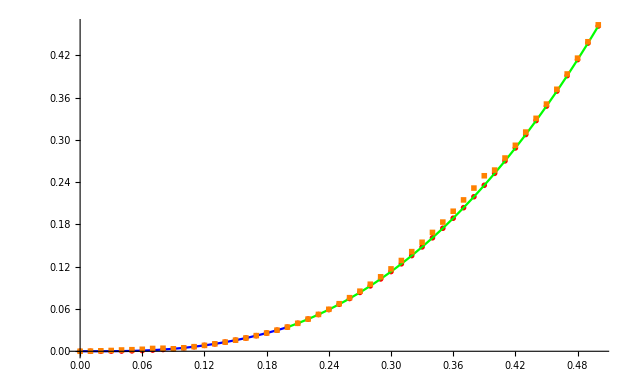

```mathematica
Show[ListPlot[tab, PlotStyle->Red,PlotMarkers->●], Plot[final,{γ,0,1/5},PlotStyle->Blue], Plot[final2,{γ,1/5,1/2},PlotStyle->Green],ListPlot[data, PlotStyle->Orange,PlotMarkers->■]]
```

## Four-qubit X-MEMS

```mathematica
f[γ_]:=If[γ<=1/9,1/9,γ];
g[γ_]:=If[γ<=1/9,1/9,(1-2γ)/7];
```

```mathematica
ρ=({{f, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, γ}, {0, g, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {γ, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, f}});
σ=({{a/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, d}, {0, b/7, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, b/7, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, b/7, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, b/7, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, b/7, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, b/7, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, b/7, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (1-a-b)/7, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, (1-a-b)/7, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (1-a-b)/7, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (1-a-b)/7, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (1-a-b)/7, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (1-a-b)/7, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (1-a-b)/7, 0}, {d, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a/2}});
HSD[ρ_,σ_]:=Tr[MatrixPower[ρ-σ,2]];
```

```mathematica
dd=HSD[ρ,σ]
```

1/7 (-1+a+b)^2+2 (-a/2+f)^2+7 (-b/7+g)^2+2 (-d+γ)^2

### Separability condition

```mathematica
Eigenvalues[PartialTranspose[σ,{2,2,2,2},{1}]]//PowerExpand//FullSimplify
```

{a/2,a/2,b/7,b/7,b/7,b/7,b/7,b/7,1/7 (1-a-b),1/7 (1-a-b),1/7 (1-a-b),1/7 (1-a-b),1/7 (1-a-b),1/7 (1-a-b),1/14 (1-a-√((-1+a+2 b)^2+196 d^2)),1/14 (1-a+√((-1+a+2 b)^2+196 d^2))}

```mathematica
E1=49 d^2-b(1-a-b)
```

-((1-a-b) b)+49 d^2

### Segment 1

```mathematica
L=dd+λ E1/.{f->1/9,g->1/9}//FullSimplify
L1=D[L,a]//FullSimplify
L2=D[L,b]//FullSimplify
L3=D[L,d]//FullSimplify
```

1/162 (2-9 a)^2+1/567 (7-9 b)^2+1/7 (-1+a+b)^2+2 (d-γ)^2+b (-1+a+b) λ+49 d^2 λ

-32/63+(9 a)/7+b (2/7+λ)

2/63 (-16+9 a+18 b)+(-1+a+2 b) λ

-4 γ+d (4+98 λ)

```mathematica
sol=Solve[{L1==0,L2==0,L3==0,E1==0},{a,b,d,λ}]
Simplify[Reduce[{L1==0,L2==0,L3==0,E1==0},{a,b,d,λ}],{0<=a<=1,0<=b<=1,0<=a+b<=1,0<=d<=a/2,0<=γ<=1/9}]
```

(1)
 |  |  |  |

(a==Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,1]||a==Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,2]||a==Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,3]||a==Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,4])&&460498 a+2368521 a^3+3136 b+44100 γ^2==39488+1848339 a^2+142884 a γ^2&&513 a≠121&&d==(9 (-1+a) γ)/(-121+513 a)&&a≠1&&λ==(16 (-2+9 a))/(63 (-1+a))

```mathematica
Solve[460498 a+2368521 a^3+3136 b+44100 γ^2==39488+1848339 a^2+142884 a γ^2,b]
```

(b→(39488-460498 a+1848339 a^2-2368521 a^3-44100 γ^2+142884 a γ^2)/3136)

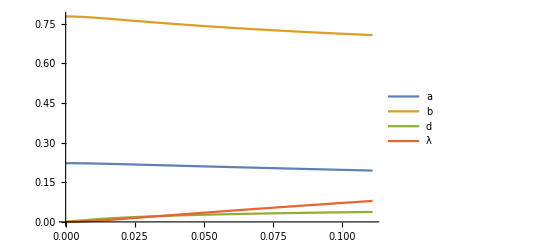

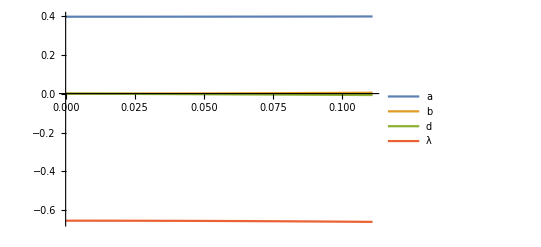

-Graphics-

-Graphics-

```mathematica
aa=Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,1];
Plot[{aa,(39488-460498 a+1848339 a^2-2368521 a^3-44100 γ^2+142884 a γ^2)/3136/.a->aa,(9 (-1+a) γ)/(-121+513 a)/.a->aa,(16 (-2+9 a))/(63 (-1+a))/.a->aa},{γ,0,1/9},PlotLegends->{a,b,d,λ}]
aa=Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,2];
Plot[{aa,(39488-460498 a+1848339 a^2-2368521 a^3-44100 γ^2+142884 a γ^2)/3136/.a->aa,(9 (-1+a) γ)/(-121+513 a)/.a->aa,(16 (-2+9 a))/(63 (-1+a))/.a->aa},{γ,0,1/9},PlotLegends->{a,b,d,λ}]
aa=Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,3];
Plot[{aa,(39488-460498 a+1848339 a^2-2368521 a^3-44100 γ^2+142884 a γ^2)/3136/.a->aa,(9 (-1+a) γ)/(-121+513 a)/.a->aa,(16 (-2+9 a))/(63 (-1+a))/.a->aa},{γ,0,1/9},PlotLegends->{a,b,d,λ}]
aa=Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,4];
Plot[{aa,(39488-460498 a+1848339 a^2-2368521 a^3-44100 γ^2+142884 a γ^2)/3136/.a->aa,(9 (-1+a) γ)/(-121+513 a)/.a->aa,(16 (-2+9 a))/(63 (-1+a))/.a->aa},{γ,0,1/9},PlotLegends->{a,b,d,λ}]
```

```mathematica
aa=Root[937024-1102500 γ^2+(-14533794+7144200 γ^2) #1+(83381805-11573604 γ^2) #1^2-208928484 #1^3+191850201 #1^4&,1];
dd/.{f->1/9,g->1/9,b->(39488-460498 a+1848339 a^2-2368521 a^3-44100 γ^2+142884 a γ^2)/3136,d->(9 (-1+a) γ)/(-121+513 a),λ->(16 (-2+9 a))/(63 (-1+a))}//FullSimplify
```

1/162 (2-9 a)^2+2 (γ-(9 (-1+a) γ)/(-121+513 a))^2+((-333440+396900 γ^2+9 a (460498+1539 a (-1201+1539 a)-142884 γ^2))^2)/5576159232+((-36352+44100 γ^2+9 a (50818+171 a (-1201+1539 a)-15876 γ^2))^2)/68841472

```mathematica
final=dd/.sol[[2]]/.{f->1/9,g->1/9}
```

7 (1/9+1/7 (-2513/4104+1/2 1-1/2 √(6315169/2105352-(343 (24535+1))/3158028-1/1-1/(113689008 1)-1/(4 √(4+1)))))^2+2 (1/9-1/(2 (1)))^2+1/7 (-1591/4104-1/2 1+1+1/1)^2+2 (γ-(1/76+31)/(-97838349 γ-100718100 γ^3))^2
 |  |  |  |

### Segment 2

```mathematica
M=dd+λ E1/.{f->γ,g->(1-2γ)/7}//FullSimplify
M1=D[M,a]//FullSimplify
M2=D[M,b]//FullSimplify
M3=D[M,d]//FullSimplify
```

1/7 (-1+a+b)^2+1/2 (a-2 γ)^2+2 (d-γ)^2+1/7 (-1+b+2 γ)^2+b (-1+a+b) λ+49 d^2 λ

a+2/7 (-1+a+b)-2 γ+b λ

2/7 (a+2 (-1+b+γ))+(-1+a+2 b) λ

-4 γ+d (4+98 λ)

```mathematica
sol2=Solve[{M1==0,M2==0,M3==0,E1==0},{a,b,d,λ}]
Simplify[Reduce[{M1==0,M2==0,M3==0,E1==0},{a,b,d,λ}],{0<=a<=1,0<=b<=1,0<=a+b<=1,0<=d<=a/2,1/9<=γ<=1/2}]
```

(1)
 |  |  |  |

(a==Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,1]||a==Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,2]||a==Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,3]||a==Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,4])&&9 a≠1+16 γ&&b==((-1+a) (-2+9 a-14 γ))/(2-18 a+32 γ)&&57 a≠1&&d==(-24+1026 a^2+b (24-48 γ)+333 γ+3472 γ^2-3 a (40+1287 γ))/(-3+171 a)&&a≠1&&λ==(16 (a-2 γ))/(7 (-1+a))

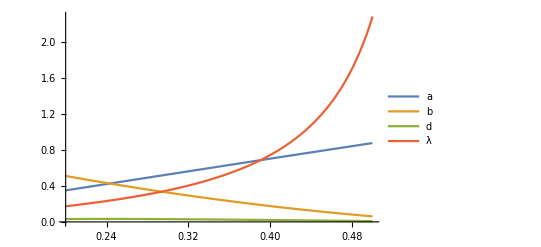

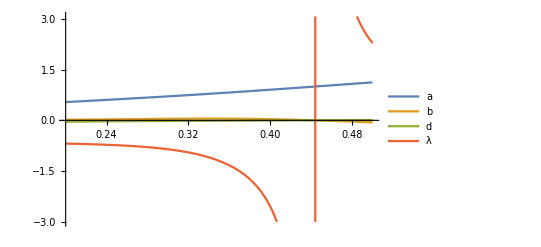

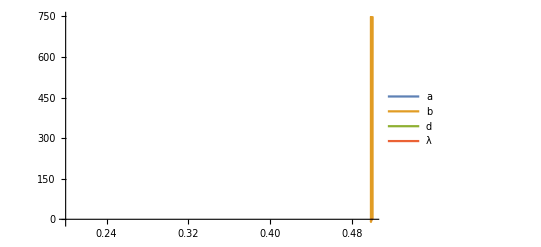

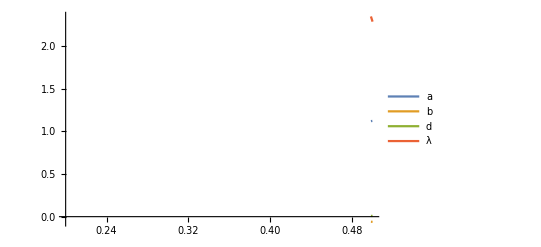

```mathematica
aa=Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,1];
Plot[{aa,((-1+a) (-2+9 a-14 γ))/(2-18 a+32 γ)/.a->aa,(-24+1026 a^2+b (24-48 γ)+333 γ+3472 γ^2-3 a (40+1287 γ))/(-3+171 a)/.b->((-1+a) (-7+25 a-36 γ))/(8-50 a+84 γ)/.a->aa,(16 (a-2 γ))/(7 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
aa=Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,2];
Plot[{aa,((-1+a) (-2+9 a-14 γ))/(2-18 a+32 γ)/.a->aa,(-24+1026 a^2+b (24-48 γ)+333 γ+3472 γ^2-3 a (40+1287 γ))/(-3+171 a)/.b->((-1+a) (-7+25 a-36 γ))/(8-50 a+84 γ)/.a->aa,(16 (a-2 γ))/(7 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
aa=Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,3];
Plot[{aa,((-1+a) (-2+9 a-14 γ))/(2-18 a+32 γ)/.a->aa,(-24+1026 a^2+b (24-48 γ)+333 γ+3472 γ^2-3 a (40+1287 γ))/(-3+171 a)/.b->((-1+a) (-7+25 a-36 γ))/(8-50 a+84 γ)/.a->aa,(16 (a-2 γ))/(7 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
aa=Root[36 γ+8120 γ^2+501760 γ^3+3110912 γ^4+(-18-8424 γ-775152 γ^2-6773760 γ^3) #1+(2133+397764 γ+5496120 γ^2) #1^2+(-67716-1969920 γ) #1^3+263169 #1^4&,4];
Plot[{aa,((-1+a) (-2+9 a-14 γ))/(2-18 a+32 γ)/.a->aa,(-24+1026 a^2+b (24-48 γ)+333 γ+3472 γ^2-3 a (40+1287 γ))/(-3+171 a)/.b->((-1+a) (-7+25 a-36 γ))/(8-50 a+84 γ)/.a->aa,(16 (a-2 γ))/(7 (-1+a))/.a->aa},{γ,1/5,1/2},PlotLegends->{a,b,d,λ}]
```

```mathematica
dd/.{f->γ,g->(1-2γ)/7,b->((-1+a) (-2+9 a-14 γ))/(2-18 a+32 γ),d->(-24+1026 a^2+b (24-48 γ)+333 γ+3472 γ^2-3 a (40+1287 γ))/(-3+171 a)/.b->((-1+a) (-2+9 a-14 γ))/(2-18 a+32 γ),λ->(16 (a-2 γ))/(7 (-1+a))}//Expand//FullSimplify
```

1/(63 (1-57 a)^2 (1-9 a+16 γ)^2)4 (81 (1-57 a)^2 a^2 (57+a (-506+1143 a))-108 a (-1+57 a) (-171+a (21653+3 a (-72035+184677 a))) γ+36 (513+a (-184948+a (12765350+9 a (-16344596+48956985 a)))) γ^2-768 (-5586+a (769817+3 a (-4306558+16804881 a))) γ^3+128 (2199985-71406546 a+408706785 a^2) γ^4-174211072 (-19+213 a) γ^5+10801086464 γ^6)

```mathematica
final2=dd/.sol2[[2]]/.{f->γ,g->(1-2γ)/7}
```

7 (1/7 (1-2 γ)+1/7 (359/456 (-1+2 γ)+1/2 √((128881 (1)^2)/51984-(49 1)/77976+1/1+(1)^(1/3)/(1403568 2^1))-1/2 √1))^2+2 (γ-(83861442+14)/(2 (1)))^2+1/7 (6+1/1)^2+2 (γ-(-19154835 γ^2+17)/(125792163 γ-503168652 γ^2+581504952 γ^3))^2
 |  |  |  |

### Minimisation

```mathematica
tab=Table[{x,Minimize[{dd/.{f->f[x],g->g[x],γ->x},E1<=0,0<=a+b<=1,0<=a<=1,0<=b<=1,0<=d<=a/2},{a,b,d}][[1]]},{x,0,1/2,0.01}]
```

{{0.,3.47628×10^-16},{0.01,8.5681×10^-6},{0.02,0.000100114},{0.03,0.000368519},{0.04,0.000872675},{0.05,0.0016483},{0.06,0.00271869},{0.07,0.00410018},{0.08,0.00580479},{0.09,0.00784175},{0.1,0.0102184},{0.11,0.0129406},{0.12,0.0161738},{0.13,0.0198355},{0.14,0.0239166},{0.15,0.0284245},{0.16,0.0333657},{0.17,0.0387465},{0.18,0.0445725},{0.19,0.0508493},{0.2,0.057582},{0.21,0.0647753},{0.22,0.072434},{0.23,0.0805625},{0.24,0.0891651},{0.25,0.098246},{0.26,0.107809},{0.27,0.117859},{0.28,0.128398},{0.29,0.139431},{0.3,0.150962},{0.31,0.162994},{0.32,0.17553},{0.33,0.188574},{0.34,0.20213},{0.35,0.216201},{0.36,0.230789},{0.37,0.245899},{0.38,0.261535},{0.39,0.277697},{0.4,0.294391},{0.41,0.31162},{0.42,0.329386},{0.43,0.347693},{0.44,0.366543},{0.45,0.38594},{0.46,0.405886},{0.47,0.426385},{0.48,0.44744},{0.49,0.469054},{0.5,0.491228}}

```mathematica
γlist=Table[i,{i,0,0.5,0.01}];
python={8.673557139182718*10^-8,0.0001756036398373184,0.0006547606116350524,0.001113441825562611,0.001809140403077336,0.0022230968883197866,0.002802425353232607,0.0039843944461276926,0.004302254694467211,0.00353994741203123,0.004878034788128538,0.006481063458371017,0.008360578892572912,0.010526502671766245,0.012987174074830963,0.015750111518035792,0.018821781483947086,0.02220764000590925,0.025912851892011257,0.02994192673683732,0.0342988448466538,0.0396736503584903,0.04567398971774678,0.05230558210676189,0.05957457815881045,0.06748689599786162,0.07604862268897926,0.08526584021188045,0.09514503998854462,0.1056923787685115,0.11691428741927812,0.12881693484306955,0.14140595444781115,0.15468669190851247,0.16866408824893675,0.183342084310972,0.19872700197453527,0.21481194099401923,0.2316066565145549,0.24907851634476097,0.257148664427986,0.27426964966790635,0.2923103189231486,0.31108243040855266,0.330582399071391,0.3508183287057656,0.3717990418295776,0.39352883462716126,0.4160167284327532,0.43926931586625617,0.46328982187231366};
data=Table[{γlist[[i]],python[[i]]},{i,1,51}]
```

{{0.,8.67356×10^-8},{0.01,0.000175604},{0.02,0.000654761},{0.03,0.00111344},{0.04,0.00180914},{0.05,0.0022231},{0.06,0.00280243},{0.07,0.00398439},{0.08,0.00430225},{0.09,0.00353995},{0.1,0.00487803},{0.11,0.00648106},{0.12,0.00836058},{0.13,0.0105265},{0.14,0.0129872},{0.15,0.0157501},{0.16,0.0188218},{0.17,0.0222076},{0.18,0.0259129},{0.19,0.0299419},{0.2,0.0342988},{0.21,0.0396737},{0.22,0.045674},{0.23,0.0523056},{0.24,0.0595746},{0.25,0.0674869},{0.26,0.0760486},{0.27,0.0852658},{0.28,0.095145},{0.29,0.105692},{0.3,0.116914},{0.31,0.128817},{0.32,0.141406},{0.33,0.154687},{0.34,0.168664},{0.35,0.183342},{0.36,0.198727},{0.37,0.214812},{0.38,0.231607},{0.39,0.249079},{0.4,0.257149},{0.41,0.27427},{0.42,0.29231},{0.43,0.311082},{0.44,0.330582},{0.45,0.350818},{0.46,0.371799},{0.47,0.393529},{0.48,0.416017},{0.49,0.439269},{0.5,0.46329}}

```mathematica
(data-tab)[[All,2]]
```

{8.67356×10^-8,0.000174428,0.000637092,0.00103074,0.00157252,0.00170422,0.00183866,0.00238438,0.00185102,2.98978×10^-6,4.71734×10^-6,7.24894×10^-6,0.0000107509,0.0000154729,0.0000214673,0.000029095,0.0000386007,0.0000500017,0.0000636648,0.0000798718,0.0000988293,4.32515×10^-6,0.0000327891,0.000176225,0.00042765,0.000780384,0.00122838,0.00176594,0.00238839,0.00309094,0.00386927,0.00471961,0.00563727,0.00661814,0.00765756,0.00875056,0.00989444,0.0110736,0.0122895,0.0135011,0.0046217,0.00409602,0.00378539,0.00349421,0.00321179,0.00293928,0.00267888,0.00242834,0.00219042,0.00196561,0.00175135}

### Plot

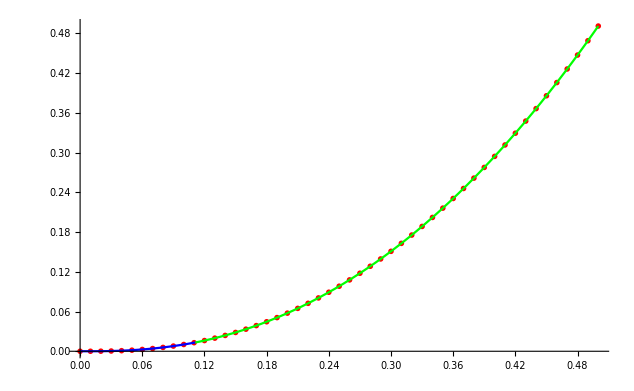

```mathematica
Show[ListPlot[tab, PlotStyle->Red,PlotMarkers->●], Plot[final,{γ,0,1/9},PlotStyle->Blue], Plot[final2,{γ,1/9,1/2},PlotStyle->Green]]
```

## n-qubit X-MEMS

```mathematica
n=3;
```

```mathematica
dd=1/(2^(n-1)-1)(1-a-b)^2+2(f-a/2)^2+1/(2^(n-1)-1)(g-b/(2^(n-1)-1))^2+2(γ-d)^2//FullSimplify
```

1/3 ((-1+a+b)^2+3/2 (a-2 f)^2+(-b/3+g)^2+6 (d-γ)^2)

### Separability condition

```mathematica
E1=(2^(n-1)-1)^2 d^2-b(1-a-b)
```

-((1-a-b) b)+9 d^2

### Segment 1

```mathematica
L=dd+λ E1/.{f->1/(2^(n-1)+1),g->1/(2^(n-1)+1)}//FullSimplify
L1=D[L,a]//FullSimplify
L2=D[L,b]//FullSimplify
L3=D[L,d]//FullSimplify
```

1/3 (3/2 (-2/5+a)^2+(1/5-b/3)^2+(-1+a+b)^2+6 (d-γ)^2)+(b (-1+a+b)+9 d^2) λ

-16/15+(5 a)/3+b (2/3+λ)

2/135 (-48+45 a+50 b)+(-1+a+2 b) λ

-4 γ+2 d (2+9 λ)

```mathematica
sol=Solve[{L1==0,L2==0,L3==0,E1==0},{a,b,d,λ}];
```

```mathematica
final=dd/.sol/.{f->1/(2^(n-1)+1),g->1/(2^(n-1)+1)};
```

### Segment 2

```mathematica
M=dd+λ E1/.{f->γ,g->(1-2γ)/(2^(n-1)-1)}//FullSimplify
M1=D[M,a]//FullSimplify
M2=D[M,b]//FullSimplify
M3=D[M,d]//FullSimplify
```

1/3 (-1+a+b)^2+1/2 (a-2 γ)^2+2 (d-γ)^2+1/27 (-1+b+2 γ)^2+b (-1+a+b) λ+9 d^2 λ

a+2/3 (-1+a+b)-2 γ+b λ

(2 a)/3+4/27 (-5+5 b+γ)+(-1+a+2 b) λ

-4 γ+2 d (2+9 λ)

```mathematica
sol2=Solve[{M1==0,M2==0,M3==0,E1==0},{a,b,d,λ}];
```

```mathematica
final2=dd/.sol2/.{f->γ,g->(1-2γ)/(2^(n-1)-1)};
```

### Plot

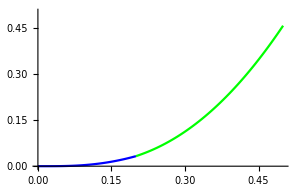

```mathematica
Show[ Plot[final[[2]],{γ,0,1/(2^(n-1)+1)},PlotStyle->Blue], Plot[final2[[2]],{γ,1/(2^(n-1)+1),1/2},PlotStyle->Green],PlotRange->{0,0.5}]
```

## X-MEMS Graph

```mathematica
dist2A=final[[1]];
dist2B=final2[[2]];
```

```mathematica
dist3A=final[[2]];
dist3B=final2[[2]];
```

```mathematica
dist4A=final[[2]];
dist4B=final2[[2]];
```

```mathematica
dist5A=final[[2]];
dist5B=final2[[2]];
```

```mathematica
dist6A=final[[2]];
dist6B=final2[[2]];
```

```mathematica
dist7A=final[[2]];
dist7B=final2[[2]];
```

```mathematica
dist8A=final[[2]];
dist8B=final2[[2]];
```

```mathematica
dist9A=final[[2]];
dist9B=final2[[2]];
```

```mathematica
Clear[n];
dist2=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->2,If[i==0,0,If[i<=1/3,dist2A/.γ->i,dist2B/.γ->i]]]},{i,0,0.5,0.001}];
dist3=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->3,If[i==0,0,If[i<=1/5,dist3A/.γ->i,dist3B/.γ->i]]]},{i,0,0.5,0.001}];
dist4=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->4,If[i==0,0,If[i<=1/9,dist4A/.γ->i,dist4B/.γ->i]]]},{i,0,0.5,0.001}];
dist5=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->5,If[i==0,0,If[i<=1/17,dist5A/.γ->i,dist5B/.γ->i]]]},{i,0,0.5,0.001}];
dist6=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->6,If[i==0,0,If[i<=1/33,dist6A/.γ->i,dist6B/.γ->i]]]},{i,0,0.5,0.001}];
dist7=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->7,If[i==0,0,If[i<=1/65,dist7A/.γ->i,dist7B/.γ->i]]]},{i,0,0.5,0.001}];
dist8=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->8,If[i==0,0,If[i<=1/129,dist8A/.γ->i,dist8B/.γ->i]]]},{i,0,0.5,0.001}];
dist9=Table[{i,If[i==0.5,(-2+2^n)/(-4+2^(3-n)+2^(1+n))/.n->9,If[i==0,0,If[i<=1/257,dist9A/.γ->i,dist9B/.γ->i]]]},{i,0,0.5,0.001}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["X-MEMS/dist2.csv",dist2//N];
Export["X-MEMS/dist3.csv",dist3//N];
Export["X-MEMS/dist4.csv",dist4//N];
Export["X-MEMS/dist5.csv",dist5//N];
Export["X-MEMS/dist6.csv",dist6//N];
Export["X-MEMS/dist7.csv",dist7//N];
Export["X-MEMS/dist8.csv",dist8//N];
Export["X-MEMS/dist9.csv",dist9//N];
```